# Friction-era VOS amplitude of a Z2 string network from nematic disclination data

Analysis notebook for D. Efstratiou, E. A. Paraskevas and L. Perivolaropoulos, "The friction-era VOS amplitude of a Z2 string network from nematic disclination data".

## 1. Setup, constants and data

```mathematica
(* ===================================================================== *)
(*  Session setup and constants                                          *)
(* ===================================================================== *)
ClearAll["Global`*"];

tStar  = 1;              (* s; reference time of Eq. (8) *)
sPrior = 0.2;            (* Sec. III C; = (1/2) Log[300/200] *)
kNR    = 2 Sqrt[2]/Pi;   (* 0.9003, Eq. (6.37) of Ref. [14]; comparison only, baseline is k = 1 *)

(* Eq. (9): assigned transport coefficient in mu m^2/s, Pf in MPa. *)
ellD[pf_] := 200 + 100 (pf - 5.6)/2.7;
```

The four quenches of Table IV. Each run carries every digitized point ("all") and the subset retained by the selection rule of Appendix A ("keep"): the first and last point of each run are dropped following Ref. [7], and additionally the second point of the ΔP = 2.00 MPa run, which begins later than the others. The reading error f is the plotted symbol half-size in natural-log units, Eq. (A1).

```mathematica
(* ===================================================================== *)
(*  Table IV: densities digitized from Fig. 2 of Chuang, Turok & Yurke,   *)
(*  Phys. Rev. Lett. 66, 2472 (1991).  Entries are {t (s), rho (mm^-2)}.  *)
(* ===================================================================== *)
quench[dP_, pf_, cell_, ferr_, colour_, drops_, pts_] :=
  Module[{keep = Delete[pts, drops]},
   <|"dP" -> dP, "Pf" -> pf, "cell" -> cell, "f" -> ferr, "ld" -> ellD[pf],
     "colour" -> colour,
     "label" -> "ΔP = " <> ToString[NumberForm[dP, {3, 2}]] <> " MPa",
     "all" -> pts, "keep" -> keep, "n" -> Length[keep]|>];

runs = <|
  "2.00" -> quench[2.00, 5.60, 158, 0.0500, RGBColor[0.40, 0.40, 0.40],
    {{1}, {2}, {-1}},
    {{3.9500, 148.0200}, {4.9170, 142.7100}, {6.2919, 137.6055},
     {7.9072, 114.1748}, {9.8462, 98.3534},  {12.4877, 80.5948},
     {15.6954, 62.8160}, {19.9083, 48.3523}, {24.7959, 36.7531},
     {31.7360, 30.5000}}],
  "2.28" -> quench[2.28, 5.88, 234, 0.0562, RGBColor[0.75, 0.10, 0.15],
    {{1}, {-1}},
    {{1.9750, 109.2800}, {3.3549, 82.1480}, {5.7002, 55.1748},
     {9.6896, 28.4948},  {16.4656, 17.7543}, {28.2350, 11.4900}}],
  "2.62" -> quench[2.62, 6.22, 234, 0.0562, RGBColor[0.10, 0.30, 0.65],
    {{1}, {-1}},
    {{0.9950, 150.8300}, {1.4879, 125.2470}, {2.2657, 86.2113},
     {3.3569, 58.5967},  {5.0204, 35.5871},  {7.5080, 21.8849},
     {11.2240, 16.6500}}],
  "4.69" -> quench[4.69, 8.29, 234, 0.0562, RGBColor[0.05, 0.45, 0.25],
    {{1}, {-1}},
    {{0.9960, 129.8000}, {1.2978, 111.8383}, {1.6763, 91.6525},
     {2.1853, 68.8140},  {2.8752, 51.0261},  {3.6472, 37.8300},
     {4.7543, 30.2371},  {6.1975, 23.8676},  {8.1520, 19.5600}}]|>;

(* Sec. III B: group 1 is the single thin-cell run, group 2 the three thick-cell runs. *)
group1  = {runs["2.00"]};
group2  = {runs["2.28"], runs["2.62"], runs["4.69"]};
allRuns = Values[runs];

Grid[Prepend[
  {#["label"], #["Pf"], #["cell"], #["ld"], #["f"], Length[#["all"]], #["n"]} & /@ allRuns,
  {"run", "Pf (MPa)", "d (μm)", "ellD (μm^2/s)", "f", "points", "retained"}],
 Frame -> All, Alignment -> Left, Background -> {None, {1 -> LightGray}}]
```

run | Pf (MPa) | d (μm) | ellD (μm^2/s) | f | points | retained
ΔP = 2.00 MPa | 5.6 | 158 | 200. | 0.05 | 10 | 7
ΔP = 2.28 MPa | 5.88 | 234 | 210.37 | 0.0562 | 6 | 4
ΔP = 2.62 MPa | 6.22 | 234 | 222.963 | 0.0562 | 7 | 5
ΔP = 4.69 MPa | 8.29 | 234 | 299.63 | 0.0562 | 9 | 7

## 2. Model and likelihood

Eq. (8) is the prediction for the density, Eq. (10) the logarithmic residual of a single digitized point, and Eq. (13) the χ^2 of one quench after its offset δ_j has been marginalized out. chi2 sums Eq. (13) over a list of quenches. These definitions are symbolic-safe: they carry no NumericQ guards, so D and ContourPlot can be applied to them directly.

```mathematica
(* ===================================================================== *)
(*  Eqs. (8), (10) and (13)                                              *)
(* ===================================================================== *)
rhoTh[t_, aA_, nu_, pf_] := 10^6/(2 aA ellD[pf] tStar) (t/tStar)^-nu;      (* Eq. (8) *)

logResid[q_, aA_, nu_] :=                                                  (* Eq. (10) *)
  (Log[#[[2]]] - Log[rhoTh[#[[1]], aA, nu, q["Pf"]]] &) /@ q["keep"];

chi2Quench[q_][aA_, nu_] :=                                                (* Eq. (13) *)
  Module[{r = logResid[q, aA, nu], f = q["f"], n = q["n"]},
   Total[r^2]/f^2 - sPrior^2 Total[r]^2/(f^2 (f^2 + n sPrior^2))];

chi2[qs_List][aA_, nu_] := Total[chi2Quench[#][aA, nu] & /@ qs];

(* Eq. (12): the shrunk per-quench offset, restored after the fit. *)
offsets[qs_List, aA_, nu_] :=
  (sPrior^2 Total[logResid[#, aA, nu]]/(#["f"]^2 + #["n"] sPrior^2) &) /@ qs;
```

## 3. Exact solution of the likelihood

By Eq. (14) every residual is R = u + ν w + Log A, with u and w fixed by the data, so χ^2 is an exact quadratic form in the two parameters (Log A, ν). The minimum therefore follows from a single linear solve, the covariance is twice the inverse Hessian, and the Δχ^2 = 1, 4, 9 intervals on A are exactly A exp(±nσ) with σ the marginal width in Log A. This replaces the FindMinimum/FindRoot calls of the original notebook, which is where its FindMinimum::lstol warnings came from.

sigmaLogAEq16 is the independent closed form of Eq. (16), valid at fixed ν; the check cell below confirms that the quadratic form reproduces the direct definition of Section 2 and that the two expressions for the conditional width agree.

```mathematica
(* ===================================================================== *)
(*  Eq. (14): chi^2 as an exact quadratic form in (lv, nv) = (Log A, nu)  *)
(* ===================================================================== *)
uwOf[q_] :=
  ({Log[#[[2]]] - Log[10^6/(2 ellD[q["Pf"]] tStar)], Log[#[[1]]/tStar]} &) /@ q["keep"];

chi2QuadQuench[q_][lv_, nv_] :=
  Module[{r = (#[[1]] + nv #[[2]] + lv &) /@ uwOf[q], f = q["f"], n = q["n"]},
   Total[r^2]/f^2 - sPrior^2 Total[r]^2/(f^2 (f^2 + n sPrior^2))];

chi2Quad[qs_List][lv_, nv_] := Total[chi2QuadQuench[#][lv, nv] & /@ qs];

(* Eq. (16): conditional width of Log A, from the retained point counts alone. *)
sigmaLogAEq16[qs_List] :=
  (Total[(#["n"]/(#["f"]^2 + #["n"] sPrior^2) &) /@ qs])^(-1/2);

(* --- exponent free: two-parameter fit ------------------------------- *)
fitFree[qs_List] :=
  Module[{lv, nv, q2, hess, grad0, lHat, nuHat, cov},
   q2    = chi2Quad[qs][lv, nv];
   hess  = D[q2, {{lv, nv}, 2}];
   grad0 = D[q2, {{lv, nv}}] /. {lv -> 0, nv -> 0};
   {lHat, nuHat} = LinearSolve[hess, -grad0];
   cov   = 2 Inverse[hess];
   <|"A" -> Exp[lHat], "nu" -> nuHat,
     "chi2min" -> (q2 /. {lv -> lHat, nv -> nuHat}),
     "N" -> Total[#["n"] & /@ qs], "nuFree" -> True,
     "sigmaLogACond" -> Sqrt[2/hess[[1, 1]]],
     "sigmaLogA" -> Sqrt[cov[[1, 1]]], "sigmaNu" -> Sqrt[cov[[2, 2]]],
     "corr" -> cov[[1, 2]]/Sqrt[cov[[1, 1]] cov[[2, 2]]],
     "offsets" -> offsets[qs, Exp[lHat], nuHat]|>];

(* --- exponent imposed ----------------------------------------------- *)
fitFixed[qs_List, nu0_: 1] :=
  Module[{lv, q2, h, g0, lHat},
   q2 = chi2Quad[qs][lv, nu0];
   h  = D[q2, {lv, 2}];
   g0 = D[q2, lv] /. lv -> 0;
   lHat = -g0/h;
   <|"A" -> Exp[lHat], "nu" -> nu0, "chi2min" -> (q2 /. lv -> lHat),
     "N" -> Total[#["n"] & /@ qs], "nuFree" -> False,
     "sigmaLogACond" -> Sqrt[2/h], "sigmaLogA" -> Sqrt[2/h],
     "sigmaNu" -> 0, "corr" -> 0,
     "offsets" -> offsets[qs, Exp[lHat], nu0]|>];

(* Delta chi^2 = n^2 interval on A; exact and asymmetric in A, Sec. III D. *)
interval[fit_, nSig_: 1] := fit["A"] Exp[{-1, 1} nSig fit["sigmaLogA"]];
```

Check: the quadratic form agrees with the direct definition of Section 2 point by point, and the conditional width agrees with Eq. (16). Both differences should be zero to machine precision.

```mathematica
Column[{
  Row[{"chi2Quad - chi2 at a test point : ",
    Chop[chi2Quad[group2][Log[7.3], 0.97] - chi2[group2][7.3, 0.97]]}],
  Row[{"sigmaLogACond - Eq. (16), group 2: ",
    Chop[fitFree[group2]["sigmaLogACond"] - sigmaLogAEq16[group2]]}],
  Row[{"sigmaLogACond - Eq. (16), group 1: ",
    Chop[fitFree[group1]["sigmaLogACond"] - sigmaLogAEq16[group1]]}]}]
```

chi2Quad - chi2 at a test point : 0
sigmaLogACond - Eq. (16), group 2: 0
sigmaLogACond - Eq. (16), group 1: 0

## 4. Results: Tables II and III

```mathematica
(* ===================================================================== *)
(*  Eqs. (3), (5) and (7)                                                *)
(* ===================================================================== *)
aOf[lam_, ce_, k_] := k (k + ce lam)/lam^2;        (* Eq. (3) *)
cOf[lam_, aA_, k_] := aA lam/k - k/lam;            (* Eq. (5) *)
lamCrit[cU_, aA_]  := (cU + Sqrt[cU^2 + 4 aA])/(2 aA);   (* Eq. (5) solved at k = 1 *)

(* --- the four baseline fits ----------------------------------------- *)
g2Free = fitFree[group2];   g2Nu1 = fitFixed[group2];
g1Free = fitFree[group1];   g1Nu1 = fitFixed[group1];

(* central value with its asymmetric interval, as quoted in the paper *)
pm[c_, up_, dn_] :=
  Row[{NumberForm[c, {4, 2}], " ",
    Style[Column[{Row[{"+", NumberForm[up, {3, 2}]}],
       Row[{"-", NumberForm[dn, {3, 2}]}]}, Spacings -> 0], 10]}];
pmFit[fit_] := pm[fit["A"], interval[fit][[2]] - fit["A"], fit["A"] - interval[fit][[1]]];

fitRow[name_, fit_] := {name, pmFit[fit],
   If[fit["nuFree"],
    Row[{NumberForm[fit["nu"], {4, 3}], " ± ", NumberForm[fit["sigmaNu"], {3, 3}]}],
    "≡ 1"],
   NumberForm[fit["chi2min"], {4, 2}], fit["N"]};

Grid[Prepend[{
   fitRow["group 2, exponent free", g2Free],
   fitRow["group 2, ν ≡ 1", g2Nu1],
   fitRow["group 1, exponent free", g1Free],
   fitRow["group 1, ν ≡ 1", g1Nu1]},
  {"fit", "A", "ν", Row[{Superscript["χ", 2], "min"}], "N"}],
 Frame -> All, Alignment -> Left, Background -> {None, {1 -> LightGray}}]
```

fit | A | ν | χ^2min | N
group 2, exponent free | 10.02 +1.30
-1.15 | 1.030 ± 0.025 | 13.59 | 16
group 2, ν ≡ 1 | 10.46 +1.29
-1.15 | ≡ 1 | 15.03 | 16
group 1, exponent free | 2.98 +0.76
-0.60 | 0.954 ± 0.041 | 5.81 | 7
group 1, ν ≡ 1 | 2.65 +0.59
-0.48 | ≡ 1 | 7.08 | 7

```mathematica
(* --- Table II: one run at a time, exponent free ---------------------- *)
tableII = fitFree[{#}] & /@ allRuns;

Grid[Prepend[
  MapThread[{#1["label"], #1["Pf"], #1["ld"], #1["cell"], #1["n"],
      NumberForm[#2["A"], {4, 2}], NumberForm[#2["nu"], {4, 3}]} &,
   {allRuns, tableII}],
  {"run", "Pf (MPa)", "ellD", "d (μm)", "n", "A", "ν"}],
 Frame -> All, Alignment -> Left, Background -> {None, {1 -> LightGray}}]
```

run | Pf (MPa) | ellD | d (μm) | n | A | ν
ΔP = 2.00 MPa | 5.6 | 200. | 158 | 7 | 2.98 | 0.954
ΔP = 2.28 MPa | 5.88 | 210.37 | 234 | 4 | 8.36 | 0.991
ΔP = 2.62 MPa | 6.22 | 222.963 | 234 | 5 | 11.01 | 1.084
ΔP = 4.69 MPa | 8.29 | 299.63 | 234 | 7 | 11.14 | 1.022

```mathematica
(* --- derived c-tilde at lambda = 1, and the fitted offsets ----------- *)
Column[{
  Style["Derived at λ = 1, exponent free (Eq. 5) — not a measurement of c~", Bold],
  Row[{"  group 2, k = 1    : c~ = ", NumberForm[cOf[1, g2Free["A"], 1], {4, 2}],
     " +", NumberForm[interval[g2Free][[2]] - g2Free["A"], {3, 2}],
     " -", NumberForm[g2Free["A"] - interval[g2Free][[1]], {3, 2}]}],
  Row[{"  group 1, k = 1    : c~ = ", NumberForm[cOf[1, g1Free["A"], 1], {4, 2}],
     " +", NumberForm[interval[g1Free][[2]] - g1Free["A"], {3, 2}],
     " -", NumberForm[g1Free["A"] - interval[g1Free][[1]], {3, 2}]}],
  Row[{"  group 2, k = kNR  : c~ = ", NumberForm[cOf[1, g2Free["A"], kNR], {4, 2}]}],
  Row[{"  group 1, k = kNR  : c~ = ", NumberForm[cOf[1, g1Free["A"], kNR], {4, 2}]}],
  "",
  Style["Fitted per-run offsets of group 2, Eq. (12)", Bold],
  Grid[Prepend[
    MapThread[{#1["label"], NumberForm[#2, {4, 3}],
        Row[{Round[100 (Exp[#2] - 1)], "%"}],
        Row[{NumberForm[#2/sPrior, {3, 2}], "σ"}]} &,
     {group2, g2Free["offsets"]}],
    {"run", "δ", "in ρ", "in units of the prior"}],
   Frame -> All, Alignment -> Left],
  "",
  Row[{"amplitude–exponent correlation: group 2 ",
    NumberForm[g2Free["corr"], {4, 3}], ",  group 1 ",
    NumberForm[g1Free["corr"], {4, 3}]}],
  Row[{"widening of sigma_LogA by (1 - corr^2)^(-1/2): group 2 ",
    NumberForm[100 (g2Free["sigmaLogA"]/g2Free["sigmaLogACond"] - 1), {3, 1}],
    "%,  group 1 ",
    NumberForm[100 (g1Free["sigmaLogA"]/g1Free["sigmaLogACond"] - 1), {3, 1}], "%"}],
  Row[{"information per quench, n/(f^2 + n s^2), ceiling 1/s^2 = ",
    NumberForm[1/sPrior^2, {4, 1}], " : ",
    NumberForm[#["n"]/(#["f"]^2 + #["n"] sPrior^2), {4, 2}] & /@ group2}]}]
```

Derived at λ = 1, exponent free (Eq. 5) — not a measurement of c~
  group 2, k = 1    : c~ = 9.02 +1.30 -1.15
  group 1, k = 1    : c~ = 1.98 +0.76 -0.60
  group 2, k = kNR  : c~ = 10.23
  group 1, k = kNR  : c~ = 2.41

Fitted per-run offsets of group 2, Eq. (12)
run | δ | in ρ | in units of the prior
ΔP = 2.28 MPa | 0.254 | 29% | 1.27σ
ΔP = 2.62 MPa | -0.158 | -15% | -0.79σ
ΔP = 4.69 MPa | -0.096 | -9% | -0.48σ

amplitude–exponent correlation: group 2 -0.294,  group 1 -0.459
widening of sigma_LogA by (1 - corr^2)^(-1/2): group 2 4.6%,  group 1 12.6%
information per quench, n/(f^2 + n s^2), ceiling 1/s^2 = 25.0 : {24.52,24.61,24.72}

## 5. Figures

Figures 3(a), 3(b), 4, 5(a), 5(b) and 6 of the paper, in that order. Styles are set once here rather than per figure. Set exportFigures = True in the last cell of this section to write PDFs into a figures/ subdirectory of the notebook's own directory.

```mathematica
(* ===================================================================== *)
(*  Shared figure styles                                                 *)
(* ===================================================================== *)
(* aA, nn, lam and tv are used as plot variables below; keep them clear. *)
ClearAll[aA, nn, lam, tv];

baseStyle    = {FontFamily -> "Times", 18};
baseStyleBig = {FontFamily -> "Times", 20};
frameStyle   = Directive[Black, AbsoluteThickness[1.2]];
bandColour   = RGBColor[0.478, 0.063, 0.125];

(* Delta chi^2 for nSig sigma with m parameters jointly: 2.30, 6.18, 11.83 at m = 2. *)
deltaChi2[nSig_, m_] := 2 InverseGammaRegularized[m/2, 1 - Erf[nSig/Sqrt[2]]];
```

Figure 3(a). The point-by-point observable A_obs = L^2/(ℓ_d t), Eq. (4) applied to each datum separately with L0 dropped. It involves no fitting: a network on the attractor gives a horizontal line whatever its amplitude. The band is the group-2 result with its ±1σ interval.

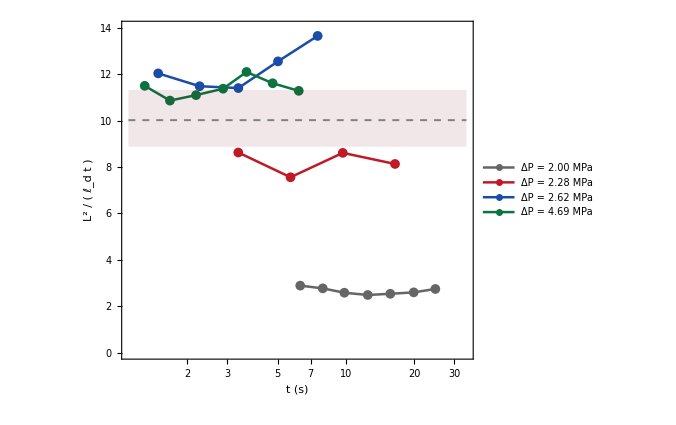

```mathematica
aObs[q_, pt_] := 10^6/(2 pt[[2]] q["ld"] pt[[1]]);   (* Eq. (4) at nu = 1, one datum *)

aObsData = Table[Function[{r}, {r[[1]], aObs[qq, r]}] /@ qq["keep"], {qq, allRuns}];

{aLo, aHi} = interval[g2Free];

fig3a = Show[
   ListLogLinearPlot[aObsData, Joined -> True, PlotMarkers -> {"●", 10},
    PlotStyle -> (Directive[#["colour"], AbsoluteThickness[1.8]] & /@ allRuns),
    PlotLegends -> Placed[#["label"] & /@ allRuns, {0.42, 0.20}]],
   Graphics[{bandColour, Opacity[0.10],
     Rectangle[{Log[1.1], aLo}, {Log[34], aHi}]}],
   Graphics[{Gray, Dashed, AbsoluteThickness[1.4],
     Line[{{Log[1.1], g2Free["A"]}, {Log[34], g2Free["A"]}}]}],
   Frame -> True, Axes -> False,
   FrameLabel -> {Style["t  (s)", 26, FontFamily -> "Times"],
     Style[Row[{Superscript["L", 2], " / ( ", Subscript["ℓ", "d"], " t )"}], 26,
      FontFamily -> "Times"]},
   FrameTicksStyle -> Directive[Black, 20],
   PlotRange -> {Log[{1.1, 34}], {0, 14}}, PlotRangeClipping -> True,
   BaseStyle -> baseStyleBig, FrameStyle -> frameStyle,
   ImageSize -> 500, AspectRatio -> 0.85]
```

Figure 3(b). The single-quench amplitudes of Table II against quench depth, with the prior-limited errors of Eq. (16) applied to one run. Band and dashed line are the three-run result of Eq. (17).

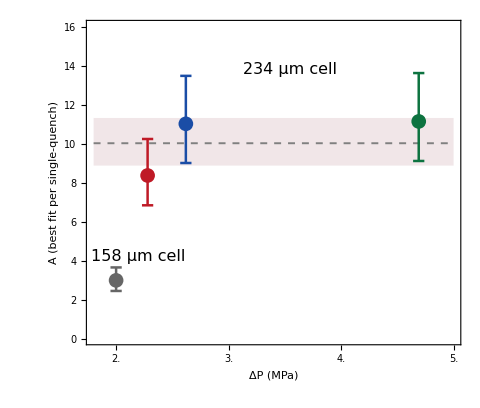

```mathematica
sigRun = sigmaLogAEq16[{#}] & /@ allRuns;
(* Table II values, i.e. each run fitted alone with its own free exponent, which
   is what the caption of Fig. 3(b) describes.  The original notebook instead held
   the exponent at the group-2 best fit, giving 2.46, 7.74, 11.76, 11.04. *)
aRun   = #["A"] & /@ tableII;

bars = Table[
   With[{x = allRuns[[i]]["dP"], lo = aRun[[i]] Exp[-sigRun[[i]]],
     hi = aRun[[i]] Exp[sigRun[[i]]]},
    {allRuns[[i]]["colour"], AbsoluteThickness[1.8],
     Line[{{x, lo}, {x, hi}}],
     Line[{{x - 0.05, lo}, {x + 0.05, lo}}],
     Line[{{x - 0.05, hi}, {x + 0.05, hi}}],
     PointSize[0.022], Point[{x, aRun[[i]]}]}], {i, Length[allRuns]}];

fig3b = Show[
   Graphics[{bandColour, Opacity[0.10], Rectangle[{1.8, aLo}, {5.0, aHi}]}],
   Graphics[{Gray, Dashed, AbsoluteThickness[1.4],
     Line[{{1.8, g2Free["A"]}, {5.0, g2Free["A"]}}]}],
   Graphics[bars],
   Graphics[{Black,
     Text[Style["158 μm cell", 16, FontFamily -> "Times"], {2.20, 4.2}],
     Text[Style["234 μm cell", 16, FontFamily -> "Times"], {3.55, 13.8}]}],
   Frame -> True, Axes -> False,
   FrameLabel -> {Style["ΔP  (MPa)", 26, FontFamily -> "Times"],
     Style["A  (best fit per single-quench)", 26, FontFamily -> "Times"]},
   FrameTicks -> {{Range[0, 16, 2], None}, {Range[2.0, 5.0, 0.5], None}},
   FrameTicksStyle -> Directive[Black, 20],
   PlotRange -> {{1.8, 5.0}, {0, 16}}, PlotRangeClipping -> True,
   BaseStyle -> baseStyleBig, FrameStyle -> frameStyle,
   ImageSize -> 480, AspectRatio -> 0.85]
```

Figure 4. The four quenches with the fitted curves. The three thick-cell runs share the amplitude of Eq. (17) and the ΔP = 2.00 MPa run that of Eq. (18); within a group the curves differ only through the assigned ℓ_d of Eq. (9) and the fitted offsets of Eq. (12), so they are not independent fits. Each curve is drawn only over the span of its own retained data. Error bars are omitted because Ref. [7] states only that its statistical errors are smaller than the plotted symbols.

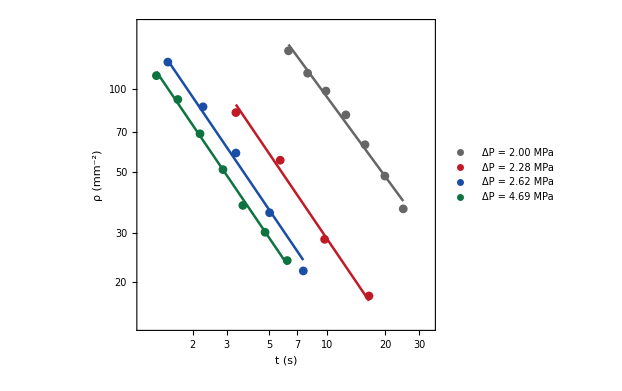

```mathematica
fitOf   = <|"2.00" -> g1Free, "2.28" -> g2Free, "2.62" -> g2Free, "4.69" -> g2Free|>;
offAll  = AssociationThread[Keys[runs] -> Join[g1Free["offsets"], g2Free["offsets"]]];

fig4curves = Table[
   Module[{q = allRuns[[i]], fit, t1, t2, amp, nu, off, pf, cc},
    fit = fitOf[Keys[runs][[i]]];
    {t1, t2} = {q["keep"][[1, 1]], q["keep"][[-1, 1]]};
    {amp, nu, pf, cc} = {fit["A"], fit["nu"], q["Pf"], q["colour"]};
    off = offAll[Keys[runs][[i]]];
    LogLogPlot[Evaluate[Exp[off] rhoTh[tv, amp, nu, pf]], {tv, t1, t2},
     PlotStyle -> Directive[cc, AbsoluteThickness[1.8]]]],
   {i, Length[allRuns]}];

fig4 = Show[fig4curves,
   ListLogLogPlot[#["keep"] & /@ allRuns, PlotMarkers -> {"●", 9},
    PlotStyle -> (#["colour"] & /@ allRuns),
    PlotLegends -> Placed[#["label"] & /@ allRuns, {0.25, 0.25}]],
   Frame -> True, Axes -> False,
   FrameLabel -> {Style["t  (s)", 22, FontFamily -> "Times"],
     Style[Row[{"ρ  (", Superscript["mm", -2], ")"}], 22, FontFamily -> "Times"]},
   FrameTicksStyle -> Directive[Black, 16],
   PlotRange -> {Log[{1.1, 34}], Log[{14, 170}]}, PlotRangeClipping -> True,
   BaseStyle -> baseStyle, FrameStyle -> frameStyle,
   ImageSize -> 460, AspectRatio -> 0.85]
```

Figure 5. Joint constraint on amplitude and exponent, contours at Δχ^2 = 2.30, 6.18 and 11.83, the 68%, 95% and 99.7% levels for two parameters jointly. Panel (a) is group 2, panel (b) group 1. Both are drawn by the same function.

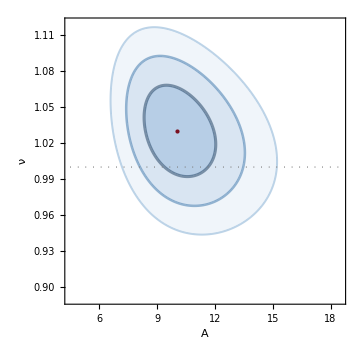

```mathematica
contourFig[fit_, qs_, {aMin_, aMax_}, {nMin_, nMax_}] :=
  Show[
   ContourPlot[Evaluate[chi2[qs][aA, nn]], {aA, aMin, aMax}, {nn, nMin, nMax},
    Contours -> (fit["chi2min"] + deltaChi2[#, 2] & /@ {1, 2, 3}),
    ContourShading -> {RGBColor[0.717, 0.808, 0.902], RGBColor[0.851, 0.898, 0.949],
      RGBColor[0.941, 0.961, 0.980], White},
    ContourStyle -> {Directive[RGBColor[0.090, 0.224, 0.361], AbsoluteThickness[2.2]],
      Directive[RGBColor[0.204, 0.439, 0.659], AbsoluteThickness[1.8]],
      Directive[RGBColor[0.478, 0.659, 0.816], AbsoluteThickness[1.4]]},
    PlotPoints -> 80],
   Epilog -> {{Gray, Dotted, AbsoluteThickness[1.2],
      Line[{{aMin, 1}, {aMax, 1}}]},
     {PointSize[Medium], bandColour, Point[{fit["A"], fit["nu"]}]}},
   Frame -> True, Axes -> False, FrameLabel -> {"A", "ν"},
   PlotRange -> {{aMin, aMax}, {nMin, nMax}}, PlotRangeClipping -> True,
   BaseStyle -> baseStyle, FrameStyle -> Directive[Black], ImageSize -> Medium];

fig5a = contourFig[g2Free, group2, {4.5, 18.5}, {0.89, 1.12}]
```

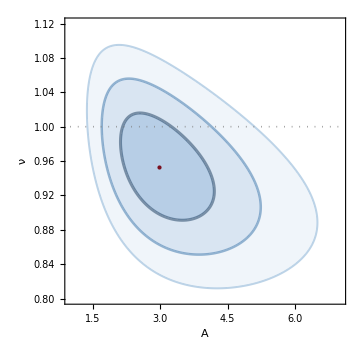

```mathematica
fig5b = contourFig[g1Free, group1, {1.0, 7.0}, {0.80, 1.12}]
```

Figure 6, the result of the paper. Every point on a given curve fits the corresponding data equally well: since χ^2 depends on k, λ and c~ only through A, the data constrain them only along c~ = Aλ/k - k/λ. The bands are the Δχ^2 = 1, 4, 9 intervals on A, marginalized over ν, mapped through that relation; they are intervals on one parameter, so the figure closes in neither direction and the bands must not be read as confidence contours in the (λ, c~) plane.

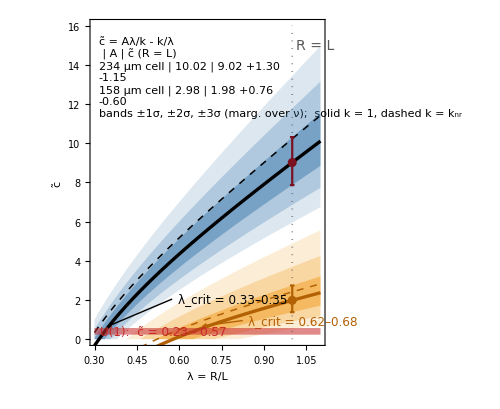

```mathematica
lamMin = 0.30; lamMax = 1.10; cMax = 16;
colBand  = RGBColor[0.25, 0.49, 0.69];   colLine  = Black;
colBand1 = RGBColor[0.95, 0.62, 0.13];   colLine1 = RGBColor[0.70, 0.38, 0.02];
colU1    = RGBColor[0.78, 0.16, 0.16];

(* Linear axes throughout: cOf is plotted directly, nothing is log-transformed. *)
band[lo_, hi_, op_, cc_] :=
  Plot[{Max[cOf[lam, lo, 1], 0], Max[cOf[lam, hi, 1], 0]}, {lam, lamMin, lamMax},
   PlotStyle -> {Opacity[0], Opacity[0]}, Filling -> {1 -> {2}},
   FillingStyle -> Directive[Opacity[op], cc], PlotPoints -> 300,
   PlotRange -> {{lamMin, lamMax}, {0, cMax}}];

ebar[xx_, c_, lo_, hi_, cc_] :=
  {cc, AbsoluteThickness[1.6], Line[{{xx, lo}, {xx, hi}}],
   Line[{{xx - 0.008, lo}, {xx + 0.008, lo}}],
   Line[{{xx - 0.008, hi}, {xx + 0.008, hi}}],
   PointSize[0.013], Point[{xx, c}]};

(* +-1, 2, 3 sigma intervals on A, exact in Log A (Sec. III D). *)
{a1lo, a1hi} = interval[g2Free, 1]; {a2lo, a2hi} = interval[g2Free, 2];
{a3lo, a3hi} = interval[g2Free, 3];
{b1lo, b1hi} = interval[g1Free, 1]; {b2lo, b2hi} = interval[g1Free, 2];
{b3lo, b3hi} = interval[g1Free, 3];

cL2 = cOf[1, g2Free["A"], 1]; cL2p = cOf[1, a1hi, 1] - cL2; cL2m = cL2 - cOf[1, a1lo, 1];
cL1 = cOf[1, g1Free["A"], 1]; cL1p = cOf[1, b1hi, 1] - cL1; cL1m = cL1 - cOf[1, b1lo, 1];

{lamCritLo, lamCritHi}   = lamCrit[#, g2Free["A"]] & /@ {0.23, 0.57};
{lamCritLo1, lamCritHi1} = lamCrit[#, g1Free["A"]] & /@ {0.23, 0.57};

legend = Column[{
    Style[Row[{Overscript["c", "~"], " = Aλ/k - k/λ"}], 13, Black],
    Grid[{{"", "A", Row[{Overscript["c", "~"], " (R = L)"}]},
      {Style["234 μm cell", colLine], Style[NumberForm[g2Free["A"], {4, 2}], colLine],
       Style[pm[cL2, cL2p, cL2m], colLine]},
      {Style["158 μm cell", colLine1], Style[NumberForm[g1Free["A"], {4, 2}], colLine1],
       Style[pm[cL1, cL1p, cL1m], colLine1]}},
     Alignment -> {Left, Center}, Spacings -> {1.4, 0.7},
     Dividers -> {{}, {2 -> GrayLevel[0.7]}}, BaseStyle -> 12],
    Style[Row[{"bands ±1σ, ±2σ, ±3σ (marg. over ν);  solid k = 1, dashed k = ",
       Subscript["k", "nr"]}], 11, Black]},
   Spacings -> 0.6, Alignment -> Left];

fig6 = Show[
   band[a3lo, a3hi, 0.18, colBand], band[a2lo, a2hi, 0.28, colBand],
   band[a1lo, a1hi, 0.50, colBand],
   band[b3lo, b3hi, 0.18, colBand1], band[b2lo, b2hi, 0.28, colBand1],
   band[b1lo, b1hi, 0.50, colBand1],
   Plot[{cOf[lam, g2Free["A"], 1], cOf[lam, g2Free["A"], kNR],
     cOf[lam, g1Free["A"], 1], cOf[lam, g1Free["A"], kNR]}, {lam, lamMin, lamMax},
    PlotStyle -> {Directive[colLine, AbsoluteThickness[2.4]],
      Directive[colLine, AbsoluteThickness[1.1], Dashed],
      Directive[colLine1, AbsoluteThickness[2.4]],
      Directive[colLine1, AbsoluteThickness[1.1], Dashed]}, PlotPoints -> 300],
   Graphics[{
     {colU1, Opacity[0.55], Rectangle[{lamMin, 0.23}, {lamMax, 0.57}]},
     {GrayLevel[0.35], Dotted, AbsoluteThickness[1.2], Line[{{1, 0}, {1, cMax}}]},
     Text[Style["R = L", 14, GrayLevel[0.35], FontFamily -> "Times"], {1.015, 15.4}, {-1, 1}],
     ebar[1.0, cL2, cOf[1, a1lo, 1], cOf[1, a1hi, 1], bandColour],
     ebar[1.0, cL1, cOf[1, b1lo, 1], cOf[1, b1hi, 1], colLine1],
     {colLine, Arrowheads[0.025], Arrow[{{0.575, 2.05}, {lamCritHi, 0.65}}]},
     Text[Style[Row[{Subscript["λ", "crit"], " = ", NumberForm[lamCritLo, {3, 2}],
         "–", NumberForm[lamCritHi, {3, 2}]}], 12, colLine, FontFamily -> "Times",
       Background -> GrayLevel[1, 0.75]], {0.595, 2.05}, {-1, 0}],
     {colLine1, Arrowheads[0.025], Arrow[{{0.825, 0.95}, {lamCritHi1, 0.68}}]},
     Text[Style[Row[{Subscript["λ", "crit"], " = ", NumberForm[lamCritLo1, {3, 2}],
         "–", NumberForm[lamCritHi1, {3, 2}]}], 12, colLine1, FontFamily -> "Times",
       Background -> GrayLevel[1, 0.75]], {0.845, 0.95}, {-1, 0}],
     Text[Style[Row[{"U(1):  ", Overscript["c", "~"], " = 0.23 - 0.57"}], 12, colU1,
       FontFamily -> "Times", Background -> GrayLevel[1, 0.85]], {0.545, 0.40}, {0, 0}],
     Text[Style[legend, FontFamily -> "Times"], {0.315, 15.5}, {-1, 1}]}],
   Frame -> True, Axes -> False,
   PlotRange -> {{lamMin, lamMax}, {0, cMax}}, PlotRangeClipping -> True,
   FrameLabel -> {{Style[Overscript["c", "~"], 22, FontFamily -> "Times"], None},
     {Style["λ = R/L", 22, FontFamily -> "Times"], None}},
   FrameTicks -> {{Automatic, None}, {Automatic, None}},
   FrameTicksStyle -> Directive[Black, 15],
   BaseStyle -> {FontFamily -> "Times", 16}, FrameStyle -> frameStyle,
   ImageSize -> 500, AspectRatio -> 0.82]
```